# Plotting and Def

```mathematica
ar= 1;
fontsize=25;
frameTicksFontSize=25;
framethick=0.005;
thick=0.008;
dash=0.05;
labelstyle=Directive[Bold,FontFamily->"Times",Black,FontSize->fontsize,SingleLetterItalics->True];options={LabelStyle->labelstyle,BaseStyle->{FontFamily->"Times",FontSize->fontsize},AspectRatio->ar,Frame->True,  FrameStyle->Directive[Black,Thickness[framethick]],FrameTicksStyle->Directive[{Thickness[0.01],FontSize->frameTicksFontSize,FontFamily->"Times"}],Axes->False, LabelStyle->Black};
mag=2;
ResourceFunction["MaTeXInstall"][];
<<MaTeX`;
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor}"}];
v[x_,mu_]:=-x^3/3-mu*x;
```

# Parameters Define

```mathematica
folderName="C:\\Users\\....\\Length_5_D_1_K_4_yc_1_Lambda_1"; (*replace with path of simulaiton output folder*)
stemCells="cell_full";
stemY="y_full";
ext=".tsv";

L=7.;
dx=0.02;
lambda = 1;
p=1;
k = 4;
d=1;
ycri=1.;
x0=20;
viewMode="minmax";  
(*"minmax" or "centered"*)

n=Floor[L/dx];
frameLen=n*n;
(* =====helpers=====*)
path[s_]:=FileNameJoin[{folderName,s<>ext}];
```

# File Reading and Writing Functions

Function for Reading Whole Frame in (for graphics)

```mathematica
(* ::Package::*)
ClearAll[ReadTSVFrame];

(*Messages*)
ReadTSVFrame::noframe="Frame `1` is beyond end of file.";
ReadTSVFrame::short="Frame `1` incomplete: expected `2` numbers, got `3`.";
ReadTSVFrame::ntime="Frame `1` has varying timestamps; using the first. Distinct times: `2`.";

Options[ReadTSVFrame]={"ColumnMajor"->False};

(*Main:give N directly;returns {frame,t}*)
ReadTSVFrame[file_String,n_Integer?Positive,nside_Integer?Positive,OptionsPattern[]]:=Module[{N=nside,s,frameSize,expected,nums,y,times,t,mat},frameSize=N^2;
expected=2 frameSize;(*value+time per grid point*)s=OpenRead[file];(*TSV is text;don't use BinaryFormat->True*)(*Skip tokens for frames 1..(n-1)*)Quiet@Check[Skip[s,Number,expected (n-1)],Close[s];Message[ReadTSVFrame::noframe,n];Return[$Failed];];
(*Read exactly this frame:y1,t1,y2,t2,...*)nums=ReadList[s,Number,expected];
Close[s];
If[Length[nums]<expected,Message[ReadTSVFrame::short,n,expected,Length[nums]];
Return[$Failed];];
y=nums[[1;; ;;2]];
times=nums[[2;; ;;2]];
t=First@times;
If[!SameQ@@times,Message[ReadTSVFrame::ntime,n,Tally[times]];];
mat=ArrayReshape[y,{N,N}];(*row-major unflattening*)If[TrueQ@OptionValue["ColumnMajor"],(*flip if you flattened column-major*)mat=Transpose[mat]];
{mat,t}];

(*Convenience:give L and dx instead of N*)
getCellFrame[ii_Integer?Positive]:=ReadTSVFrame[path[stemCells],ii, n];
getResFrame[ii_Integer?Positive]:=ReadTSVFrame[path[stemY],ii, n];
```

Reading Positional Data In

```mathematica
(* ::Package::*)
ClearAll[ExtractCellsAndResources];

(*linear index->{i,j}*)
linToIJ[pos_Integer?Positive,N_Integer?Positive,colMajor_:False]:=If[colMajor,{Mod[pos-1,N]+1,Quotient[pos-1,N]+1},{Quotient[pos-1,N]+1,Mod[pos-1,N]+1}];

Options[ExtractCellsAndResources]={"ColumnMajor"->False,(*set True if frames were flattened column-major*)"StartFrame"->1,(*1-based start frame*)"MaxFrames"->Infinity,(*stop after this many frames*)"ShowProgress"->True,(*show a single updating progress readout*)"ProgressEvery"->10,(*update every k frames*)"ProgressLabel"->"Reading frame"};

(*Returns {positionsByFrame,resourcesByFrame,timesByFrame}*)
ExtractCellsAndResources[maskFile_String,resFile_String,nside_Integer?Positive,OptionsPattern[]]:=Module[{N=nside,frameSize=nside^2,sMask,sRes,startF=Max[1,OptionValue["StartFrame"]],maxF=OptionValue["MaxFrames"],colMajQ=TrueQ@OptionValue["ColumnMajor"],showQ=TrueQ@OptionValue["ShowProgress"],step=Max[1,OptionValue["ProgressEvery"]],label=OptionValue["ProgressLabel"],positionsBag=Internal`Bag[],resourcesBag=Internal`Bag[],timesBag=Internal`Bag[],framesRead=0,preSkip,maskPairs,negIdx,posIJ,tFrame,prev,needSkip,line,y,sk,(*progress state*)feQ=($FrontEnd=!=Null),display=Missing["NotStarted"],updateProgress,runBody,result},(*progress updater:notebook uses Monitor via'display',terminal overwrites the same line*)updateProgress[frame_Integer]:=If[showQ,If[feQ,(display=frame),WriteString[$Output,"\r"<>label<>": "<>ToString[frame]]]];
sMask=OpenRead[maskFile];
sRes=OpenRead[resFile];
(*fast-forward to the requested start frame*)preSkip=(startF-1) frameSize;
If[preSkip>0,sk=Skip[sMask,Record,preSkip];If[sk===$Failed,Close/@{sMask,sRes};Return[{{},{},{}}]];
sk=Skip[sRes,Record,preSkip];If[sk===$Failed,Close/@{sMask,sRes};Return[{{},{},{}}]];];
runBody:=(While[framesRead<maxF,(*1) mask frame*)maskPairs=ReadList[sMask,{Number,Number},frameSize];
If[Length[maskPairs]<frameSize,Break[]];
tFrame=maskPairs[[1,2]];
negIdx=Flatten@Position[maskPairs[[All,1]],_?Negative];
posIJ=linToIJ[#,N,colMajQ]&/@negIdx;
(*2) resource lines only at those indices*)prev=0;
Module[{vals={}},If[Length[negIdx]>0,Do[needSkip=negIdx[[k]]-prev-1;
If[needSkip>0,sk=Skip[sRes,Record,needSkip];If[sk===$Failed,Break[]]];
line=Read[sRes,Record];If[line===EndOfFile,Break[]];
y=ToExpression@First@StringSplit[line,"\t",2];(*resource;ignore time*)AppendTo[vals,y];
prev=negIdx[[k]];,{k,Length[negIdx]}]];
needSkip=frameSize-prev;
If[needSkip>0,sk=Skip[sRes,Record,needSkip];Null];
Internal`StuffBag[positionsBag,posIJ];
Internal`StuffBag[resourcesBag,vals];
Internal`StuffBag[timesBag,tFrame];];
framesRead++;
If[Mod[framesRead,step]==0||framesRead==1,updateProgress[startF+framesRead-1]];];);
result=If[showQ&&feQ,Monitor[runBody,Row[{label,": ",display}]],(runBody;Null)];
Close/@{sMask,sRes};
If[showQ&&!feQ,WriteString[$Output,"\n"]];(*newline after terminal progress*){Internal`BagPart[positionsBag,All],Internal`BagPart[resourcesBag,All],Internal`BagPart[timesBag,All]}];

{posByFrame,resByFrame, times}=ExtractCellsAndResources[path[stemCells],path[stemY],n,"ShowProgress"->True,"ProgressEvery"->10 (*update every 10 frames*)
];
numFrames = Length[times];
```

Writing Graph Data

```mathematica
(* ::Package::*)
ClearAll[SaveTwoColumnTSV];
Options[SaveTwoColumnTSV]={"Header"->None,(*e.g.{"q","S(q)"}*)"Append"->False,(*append to existing file?*)"Format"->(ToString[#,InputForm]&)  (*how to stringify numbers*)};

SaveTwoColumnTSV::len="q and s must have the same number of elements (got `1` and `2`).";

SaveTwoColumnTSV[file_String,q_List,s_List,OptionsPattern[]]:=Module[{qf=Flatten[q],sf=Flatten[s],n=0,fmt=OptionValue["Format"],stream,header=OptionValue["Header"],appendQ=TrueQ@OptionValue["Append"]},n=Length[qf];
If[n=!=Length[sf],Message[SaveTwoColumnTSV::len,n,Length[sf]];Return[$Failed]];
stream=If[appendQ,OpenAppend[file],OpenWrite[file]];
If[header=!=None&&!appendQ,WriteString[stream,StringRiffle[header,"\t"],"\n"]];
Do[WriteString[stream,fmt[qf[[i]]],"\t",fmt[sf[[i]]],"\n"],{i,1,n}];
Close[stream];
file];
```

# Graphics

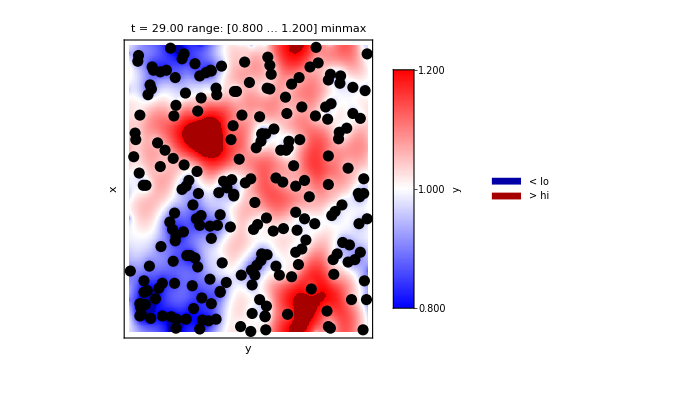

```mathematica
frameGraphic[ii_Integer?Positive,lo_Real,hi_Real]:=Module[{yM,cM,negPos,coords,cf,blendCF,img,legendGrad,legendCaps},
{yM,t}=getResFrame[ii];
{cM, t}=getCellFrame[ii];
(*hard-capped diverging map for the image*)cf[z_]:=With[{u=(z-lo)/(hi-lo)},Which[u<=0,Darker[Blue,0.35],(*cap low*)u>=1,Darker[Red,0.35],(*cap high*)True,Blend[{Blue,White,Red},u]]];
(*same blend without caps,for a clean gradient legend*)blendCF[u_]:=Blend[{Blue,White,Red},u];
(*positions of alive cells (negative cM);place at cell centers,top-left flip*)negPos=Position[cM,_?Negative];
coords=N@Transpose@{(negPos[[All,2]]-0.5)*dx,(n-negPos[[All,1]]+0.5)*dx};
(*single ArrayPlot;overlay dots via Epilog instead of Show[]*)img=ArrayPlot[yM,DataRange->{{0,L},{0,L}},ColorFunction->(cf[#]&),ColorFunctionScaling->False,(*pass raw values to cf*)PlotRange->All,(*don't clip;cf handles caps*)Frame->True,FrameLabel->{"x","y"},AspectRatio->1,Epilog->{Black,PointSize[0.02],Point[coords]},PlotLabel->Row[{"t = ",NumberForm[times[[ii]],{6,2}],"   range: [",NumberForm[lo,{6,3}]," … ",NumberForm[hi,{6,3}],"]   ",viewMode}]];
(*gradient legend for in-range values*)(*gradient legend for in-range values (rescale z->[0,1])*)legendGrad=BarLegend[{Function[z,Blend[{Blue,White,Red},Rescale[z,{lo,hi}]]],{lo,hi}},LegendLabel->"y",LabelStyle->Smaller,Ticks->{{lo,NumberForm[lo,{5,3}]},{ycri,Style[NumberForm[ycri,{5,3}],GrayLevel[0.3]]},{hi,NumberForm[hi,{5,3}]}}];
(*swatches explaining hard caps*)legendCaps=SwatchLegend[{Darker[Blue,0.35],Darker[Red,0.35]},{"< lo","> hi"},LegendLayout->"Column",LabelStyle->Smaller];
Legended[img,Placed[Column[{legendGrad,legendCaps},Spacings->0.6],Right]]]


(* =====simple slider viewer=====*)
frameGraphic[30,0.8,1.2]
```

# Number and Mu

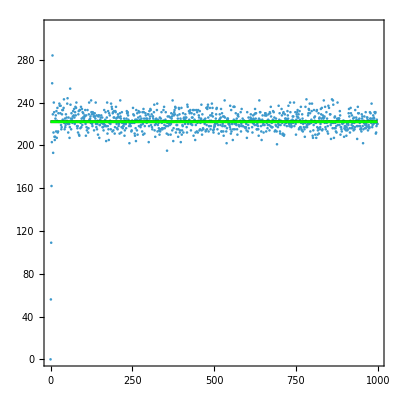

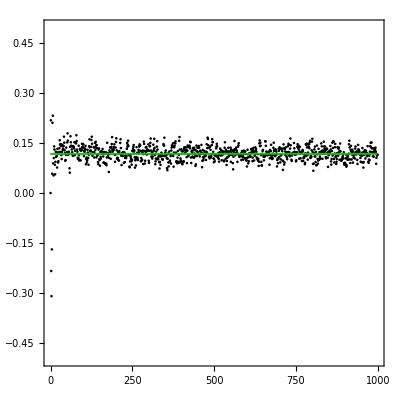

```mathematica
(*---derive time axis/counts from frames---*)

numframes=Length[times];

time=times;
ttotal=Last[time];

(*---number of cells and mean mu per frame (2D)---*)
ntot=Table[Module[{negPos=posByFrame[[i]]},
{time[[i]],Length[negPos]}],{i,1,numframes}];

mu=Table[Module[{yvals = resByFrame[[i]]},
muv=If[yvals==={},0.,ycri-Mean[yvals]];
{time[[i]],muv}],{i,1,numframes}];


μtheo0=(π^2*lambda^2*ycri^2)/(4*k^2);

μtheo=μval/. FindRoot[k/(ycri-μval)==(lambda/Sqrt[μval])*ArcTan[Abs[x0]/Sqrt[μval]],{μval,0.01}];

μnum=Mean[mu[[All,2]][[Floor[numframes/2];;numframes]]];

nss2=L*L*k/(ycri-μtheo);
nss3=L*L*k/(ycri-μnum);
numsites=n*n;
fracoc=nss3/numsites;

(*---labels (unchanged;assumes MaTeX,mag,options exist)---*)
framelabelx={MaTeX["\\text{time}",Magnification->mag],Rotate[MaTeX["N_{tot}",Magnification->mag],90 Degree]};
framelabelmu={MaTeX["\\text{time}",Magnification->mag],Rotate[MaTeX["\\bar{\\mu}",Magnification->mag],90 Degree]};

(*---plots (unchanged)---*)
Labeled[Show[ListPlot[ntot,PlotRange->{All,{0,1.4*nss2}},Evaluate[options]],Plot[{nss2,nss3},{t,0,ttotal},PlotStyle->{Black,Green}]],framelabelx,{Bottom,Left},Spacings->{-0.2,-0.2}]

Labeled[Show[ListPlot[{mu},PlotRange->{All,{-0.5,0.5}},Evaluate[options],PlotStyle->{Black,Blue}],Plot[{μtheo,μnum},{t,0,ttotal},PlotStyle->{{Black,Thick},{Green,Thick},{Green,Thick}}]],framelabelmu,{Bottom,Left},Spacings->{-0.5,-0.5}]
```

# Structure Factor, k-space

Defining K-List and MinIndex

```mathematica
mintime=22;
indexmin=First@Nearest[time->Range[Length[time]],mintime];

klist=Table[{(2 π/L) i,(2 π/L)j },{i,0,Floor[L/(16 dx)]}, {j,0,Floor[L/(16dx)]}];
kAmp=Flatten[Table[Norm[{(2 π/L) i,(2 π/L)j }],{i,0,Floor[L/(16dx)]}, {j,0,Floor[L/( 16dx)]}]];


framelabelk={MaTeX["k",Magnification->mag],Rotate[MaTeX["S\\left(k\\right)",Magnification->mag],90 Degree]};
framelabellog={MaTeX["k",Magnification->mag],Rotate[MaTeX["S\\left(k\\right)",Magnification->mag],90 Degree],MaTeX["\\text{Log-Log}",Magnification->mag]};
frametickslogk={{{0,0.01,0.1,0.5,1,1.5},None},{{0,{(2*π*1)/L,MaTeX["\\frac{2\\pi}{L}",Magnification->mag]},{(16*π)/L,MaTeX["\\frac{16\\pi}{L}",Magnification->mag]},{(8*π)/L,MaTeX["\\frac{8\\pi}{L}",Magnification->mag]},{(2*π*k/(ycri-μnum))/2,MaTeX["\\frac{2\\pi\\rho^*}{2}",Magnification->mag]}},None}};
frameticksk={{{0,0.5,1,1.5},None},{{0,{(2*π*1)/L,MaTeX["\\frac{2\\pi}{L}",Magnification->mag]},{2*π*k/(ycri-μnum),MaTeX["2\\pi\\rho^*",Magnification->mag]}},None}};
```

Calculating Structure Factor

```mathematica
fun[Q_]:=(1+Q^2)/Q;
ω0=√((π*p)/(2*μnum^(3/2)));
ωgam[q_]:=π/(2*√μnum)*(p/ycri+d*q^2)
theo[q_]:=1/ω0*fun[ωgam[q]/ω0];

msf=ConstantArray[0.,{Length[klist],Length[klist[[1]]]}];

(*Main loop with Table*)
meanntot=Mean[Part[ntot,indexmin;;numFrames,2]];
(*Do[Module[{subx,poslist,phaseSum},
poslist=dx*posByFrame[[i]];(*positions in real units*)If[Length[poslist]>0,phaseSum=Table[Table[Total[Exp[I ki.poslistᵀ]], {ki , k}],{k,klist}];
msf+=Abs[phaseSum]^2/meanntot;  (*accumulate MSF*)];],{i,indexmin,numframes}];*)

updateEvery=50;      (*change this manually*)
prog=indexmin-1;   (*init shown value*)

Monitor[Do[If[Mod[i-indexmin,updateEvery]==0||i==indexmin,prog=i];
Module[{subx,poslist,phaseSum},
poslist=dx*posByFrame[[i]];(*positions in real units*)
If[Length[poslist]>0,
phaseSum=Table[Table[Total[Exp[I ki.Transpose[poslist]]],{ki,k}],{k,klist}];
msf+=Abs[phaseSum]^2/meanntot;  (*accumulate MSF*)];],{i,indexmin,numframes}],
Row[{"Reading frame: ",prog}]];


(*Normalize MSF*)
msf=msf/(numframes-indexmin+1);
msf[[1]][[1]]=msf[[1]][[1]]-meanntot;

(*Combine with k values*)
msfData=Transpose[{Flatten[kAmp],Flatten[msf]}];

(*Theoretical Structure Factor for comparison*)
theoreticalS[q_]:=theo[q]  (*using the existing theoretical function*)
```

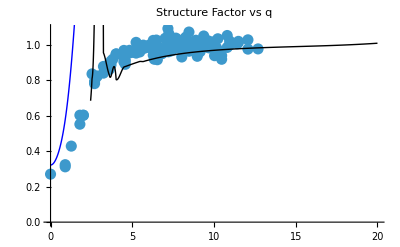

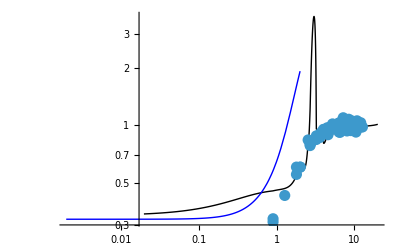

```mathematica
(*Plot the results:Experimental vs Theoretical structure factor*)
Labeled[Show[ListPlot[msfData,PlotRange->{{0,20}, All},PlotStyle->PointSize[0.02],FrameTicks->frameticksk,PlotLabel->"Structure Factor vs q"], Plot[Sdif[q],{q, 0,2}, PlotStyle->{Thick, Blue}], Plot[interpotheo[q],{q, 0,20}, PlotStyle->{Thick, Black}]],framelabelk,{Bottom,Left},Spacings->{-0.2,-0.2}]

(*Log-log plot for structure factor*)
Labeled[Show[LogLogPlot[interpotheo[q],{q, 0,20},PlotRange->All, PlotStyle->{Thick, Black}],LogLogPlot[Sdif[q],{q, 0,2},PlotRange->All, PlotStyle->{Thick, Blue}],ListLogLogPlot[msfData,PlotRange->{{0, 20}, All},PlotStyle->PointSize[0.02],FrameTicks->frametickslogk,PlotLabel->"Log-Log Plot of Structure Factor vs |q|"]],framelabellog,{Bottom,Left,Top},Spacings->{-0.2,-0.2}]
```

Saving Plot Data

```mathematica
SaveTwoColumnTSV[path["StructureFactorNum"],Flatten[kAmp],Flatten[msf]];
```

# Theoretical Numerically-Integrated Structure Factor

```mathematica
powerscale[ω_,omega0_,ξ_]:=(4* Sin[ (ω*omega0)/2]^2*(ξ^2+ω^2))/((ω^2-(1-(1+Cos[ω*omega0])/(2(1-(ω^2*omega0^2)/π^2))))^2+(ω*ξ+(Sin[ω*omega0]/(2(1-(ω^2*omega0^2)/π^2))))^2);

powerscale2[ω_,ξ_]:=(4*(ξ^2+ω^2))/((ω^2-1)^2+(ω*ξ)^2);
fun[Q_]:=(1+Q^2)/Q;
ω0=√((π*p)/(2*μnum^(3/2)));
ωgam[q_]:=π/(2*√μnum)*(p/ycri+d*q^2);
theo[q_]:=1/ω0*fun[ωgam[q]/ω0];

ω02=√((π*p)/(2*μtheo^(3/2)));
ωgam2[q_]:=π/(2*√μtheo)*(p/ycri+d*q^2)
theo2[q_]:=1/ω02*fun[ωgam2[q]/ω02];
powerscale3[ω_,omega0_,q_]:=(4* Sin[ ω/2]^2*(ωgam[q]^2+ω^2))/((ω^2-(1-(1+Cos[ω])/(2(1-ω^2/π^2)))*omega0^2)^2+(ω*ωgam[q]+omega0^2(Sin[ω]/(2(1-ω^2/π^2))))^2);

omcutoff=100;
omcutoff2=3000;

kAmpUni = DeleteDuplicates[kAmp];
NIntegrate[1/(π*ω0)*powerscale[ω,ω0,ωgam[klist[[3]]]/ω0],{ω,0,omcutoff}];
NIntegrate[1/(2*π*ω0)*powerscale2[ω,ωgam[klist[[3]]]/ω0],{ω,0,omcutoff}];
NIntegrate[1/π*powerscale3[ω,ω0,klist[[3]]],{ω,0,omcutoff2}];

numk=Length[kAmpUni]-1;
theofull=Table[{0,0},numk];
theofull2=Table[{0,0},numk];
theoaprox=Table[{0,0},numk];
theofull2b=Table[{0,0},numk];

For[t=1,t<=numk,t++,
q=kAmpUni[[t]];
theofull[[t]][[1]]=q;
theoaprox[[t]][[1]]=q;
theofull2b[[t]][[1]]=q;
theofull[[t]][[2]]=NIntegrate[1/(π*ω0)*powerscale[ω,ω0,ωgam[q]/ω0],{ω,0,omcutoff}];
theofull2[[t]][[2]]=NIntegrate[1/π*powerscale3[ω,ω0,q],{ω,0,omcutoff2}];
theofull2b[[t]][[2]]=NIntegrate[1/(π*ω02)*powerscale[ω,ω0,ωgam2[q]/ω02],{ω,0,omcutoff}];
]

interpotheo=Interpolation[theofull];
interpotheo2=Interpolation[theofull2b];
```